```mathematica
ClearAll["Global`*"];
```

```mathematica
(*ЗАДАЧА 1*)
```

```mathematica
λ:=1.6;
```

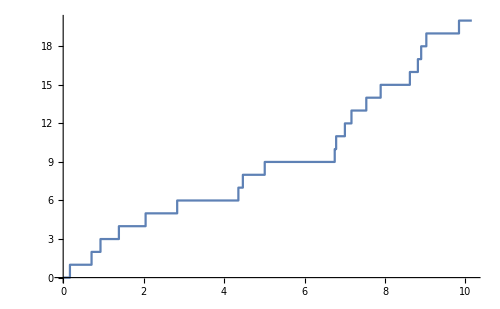

```mathematica
traect=RandomFunction[PoissonProcess[λ],{0,10},1];
ListStepPlot[traect,ImageSize->500]
```

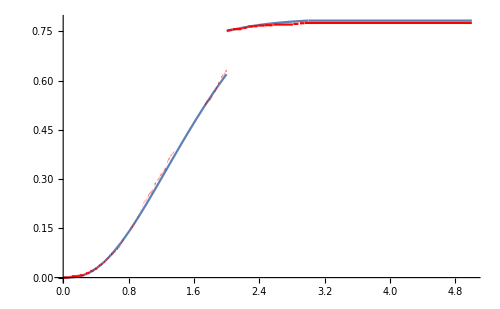

```mathematica
F[t_]:=Piecewise[{{0,t≤0},{1-(1+λ t+(λ t)^2/2)E^(-λ t),0<t≤2},{1-2 λ^2 E^(-2λ)-E^(-λ t),2<t≤3},{1-2 λ^2 E^(-2λ)-E^(-3λ),t>3}}];
FTeor=Plot[F[t],{t,0,5}];tau[s_]:=Piecewise[{{s[[4,1]],s[[4,1]]<2 },{2,s[[2,1]]≤2&&s[[3,1]]≥2},{s[[2,1]],2<s[[2,1]]≤3}},100];sample=Table[tau[RandomFunction[PoissonProcess[λ],{0,100}]["Path"]],1000];
SampleDist=EmpiricalDistribution[sample];
FEmp=Plot[CDF[SampleDist,x],{x,0,5},PlotStyle->Red];Show[FTeor,FEmp,ImageSize->500,PlotRange->All]
```

```mathematica
(*ЗАДАЧА 2*)
```

```mathematica
P=N[{{0,2/3,1/3},{2/9,5/9,2/9},{1/3,2/3,0}}];
MatrixForm[P]
```

(0. | 0.666667 | 0.333333
0.222222 | 0.555556 | 0.222222
0.333333 | 0.666667 | 0.)

```mathematica
PI={0.2,0.6,0.2};
Pτ=MatrixPower[P,τ];
Kξ=FullSimplify[(∑_(k=1)^3 ∑_(l=1)^3 k l PI[[k]]Pτ[[k,l]])-4]
```

-4.+0.4 (-0.333333)^τ+1.38778×10^-16 (-0.111111)^τ+4. 1.^τ

```mathematica
Subscript[p, 0]={1/3,1/3,1/3};
For[i=1,i≤10,i++,Subscript[p, i]=Subscript[p, i-1].P; Print[Subscript[p, i]];]
```

{0.185185,0.62963,0.185185}

{0.201646,0.596708,0.201646}

{0.199817,0.600366,0.199817}

{0.20002,0.599959,0.20002}

{0.199998,0.600005,0.199998}

{0.2,0.599999,0.2}

{0.2,0.6,0.2}

{0.2,0.6,0.2}

{0.2,0.6,0.2}

«1 more identical outputs»

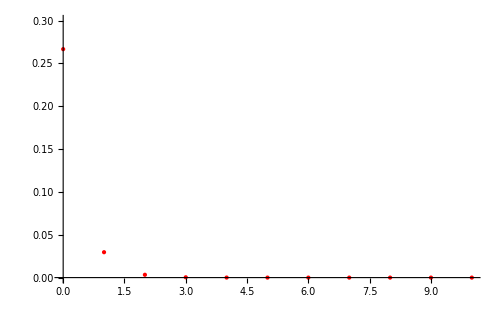

```mathematica
For[i=0,i≤10,i++,Subscript[z, i]={i,Norm[PI-Subscript[p, i],Infinity]};];ListPlot[Table[Subscript[z, i],{i,0,10}],PlotRange->{0,0.3},ImageSize->500,PlotStyle->Directive[Red,PointSize[Large]]]
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*ЗАДАЧА 3*)
```

```mathematica
λ:=4;ν:=3;T=3;
```

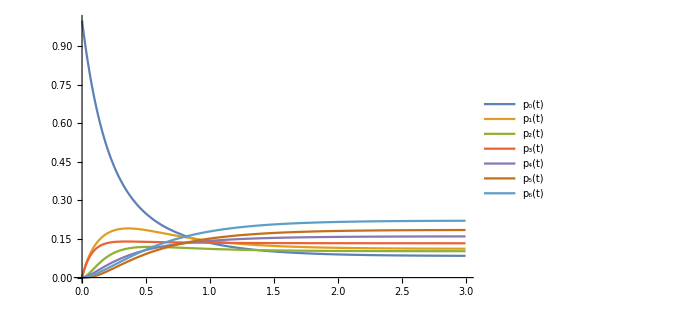

```mathematica
value={Subscript[p, 0][t],Subscript[p, 1][t],Subscript[p, 2][t],Subscript[p, 3][t],Subscript[p, 4][t],Subscript[p, 5][t],Subscript[p, 6][t]};
dots={{Subscript[p, 0]'[t]},{Subscript[p, 1]'[t]},{Subscript[p, 2]'[t]},{Subscript[p, 3]'[t]},{Subscript[p, 4]'[t]},{Subscript[p, 5]'[t]},{Subscript[p, 6]'[t]}};
sist={{-λ Subscript[p, 0][t]+ν Subscript[p, 1][t]},{-(λ+ν)Subscript[p, 1][t]+λ/2 Subscript[p, 0][t]+2ν Subscript[p, 2][t]},{-(λ+2ν)Subscript[p, 2][t]+λ/2 Subscript[p, 1][t]+2ν Subscript[p, 3][t]},{-(λ+2ν)Subscript[p, 3][t]+λ/2(Subscript[p, 2][t]+Subscript[p, 0][t])+2ν Subscript[p, 4][t]},{-(λ+2ν)Subscript[p, 4][t]+λ/2(Subscript[p, 3][t]+Subscript[p, 1][t])+2ν Subscript[p, 5][t]},{-(λ+2ν)Subscript[p, 5][t]+λ/2(Subscript[p, 4][t]+Subscript[p, 2][t])+2ν Subscript[p, 6][t]},{-2ν Subscript[p, 6][t]+λ/2(Subscript[p, 4][t]+Subscript[p, 3][t])+λ Subscript[p, 5][t]}};
init={{Subscript[p, 0][0]==1},{Subscript[p, 1][0]==0},{Subscript[p, 2][0]==0},{Subscript[p, 3][0]==0},{Subscript[p, 4][0]==0},{Subscript[p, 5][0]==0},{Subscript[p, 6][0]==0}};sol=NDSolve[{dots==sist,init},value,{t,0,T}];Plot[{value[[1]]/.sol,value[[2]]/.sol,value[[3]]/.sol,value[[4]]/.sol,value[[5]]/.sol,value[[6]]/.sol,value[[7]]/.sol},{t,0,T},ImageSize->500,PlotRange->All,PlotLegends->{"p_0(t)","p_1(t)","p_2(t)","p_3(t)","p_4(t)","p_5(t)","p_6(t)"}]
```

```mathematica
(*Вероятность того, что не будет очереди в момент t*)
```

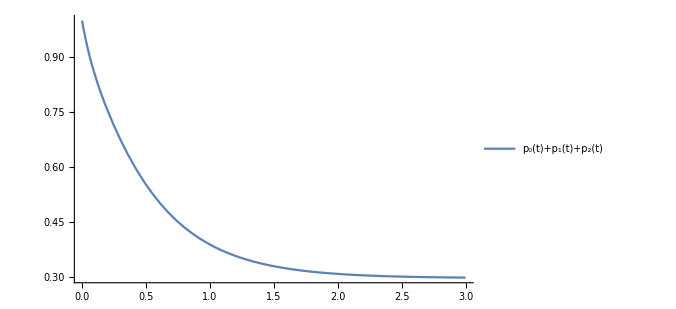

```mathematica
Plot[(Subscript[p, 0][t]+Subscript[p, 1][t]+Subscript[p, 2][t])/.sol,{t,0,T},ImageSize->500,PlotRange->All,PlotLegends->{"p_0(t)+p_1(t)+p_2(t)"}]
```

```mathematica
(*NDSolve[{Subscript[p, 0]'[t]== -λ Subscript[p, 0][t]+νSubscript[p, 1][t],Subscript[p, 1]'[t]==-(λ+ν)Subscript[p, 1][t]+2ν Subscript[p, 2][t]+λ/2 Subscript[p, 0][t],Subscript[p, 2]'[t]==2 Subscript[p, 1][t]-10 Subscript[p, 2][t]+6 Subscript[p, 3][t],Subscript[p, 3]'[t]==-(λ+2ν)Subscript[p, 3][t]+λ/2(Subscript[p, 2][t]+Subscript[p, 0][t])+2ν Subscript[p, 4][t],Subscript[p, 4]'[t]==-(λ/2+2ν)Subscript[p, 4][t]+λ/2(Subscript[p, 3][t]+Subscript[p, 1][t])+2ν Subscript[p, 5][t],Subscript[p, 5]'[t]== -(λ/2+2ν)Subscript[p, 5][t]+λ/2(Subscript[p, 4][t]+Subscript[p, 2][t])+2ν Subscript[p, 6][t],Subscript[p, 6]'[t]== -2ν Subscript[p, 6][t]+λ/2(Subscript[p, 5][t]+Subscript[p, 3][t]),Subscript[p, 0][0]==1,Subscript[p, 1][0]==0,Subscript[p, 2][0]==0,Subscript[p, 3][0]==0,Subscript[p, 4][0]==0,Subscript[p, 5][0]==0,Subscript[p, 6][0]==0},{Subscript[p, 0][t],Subscript[p, 1][t],Subscript[p, 2][t],Subscript[p, 3][t],Subscript[p, 4][t],Subscript[p, 5][t],Subscript[p, 6][t]},{t,0,T}]*)
```

```mathematica
R[t_]=Subscript[p, 0][t]/.sol;
```

```mathematica
R[T]
```

{0.103415}

```mathematica
Q[t_]=(Subscript[p, 0][t]+Subscript[p, 1][t]+Subscript[p, 2][t])/.sol;
```

```mathematica
Q[T]
```

{0.36718}

```mathematica
(*Стационарное распределение*)
```

```mathematica
SOL=NSolve[sist==0&&Subscript[p, 0][t]+Subscript[p, 1][t]+Subscript[p, 2][t]+Subscript[p, 3][t]+Subscript[p, 4][t]+Subscript[p, 5][t]+Subscript[p, 6][t]==1,value][[1]]
```

{p_0[t]→0.0838895,p_1[t]→0.111853,p_2[t]→0.102532,p_3[t]→0.133602,p_4[t]→0.160529,p_5[t]→0.185731,p_6[t]→0.221864}

```mathematica
(*SOL=NSolve[-λ Subscript[x, 0]+ν Subscript[x, 1]==0&&-(λ+ν)Subscript[x, 1]+λ/2 Subscript[x, 0]+2ν Subscript[x, 2]==0&&-(λ+2ν)Subscript[x, 2]+λ/2 Subscript[x, 1]+2ν Subscript[x, 3]==0&&-(λ+2ν)Subscript[x, 3]+λ/2(Subscript[x, 2]+Subscript[x, 0])+2ν Subscript[x, 4]==0&&-(λ/2+2ν)Subscript[x, 4]+λ/2(Subscript[x, 3]+Subscript[x, 1])+2ν Subscript[x, 5]==0&&-(λ/2+2ν)Subscript[x, 5]+λ/2(Subscript[x, 4]+Subscript[x, 2])+2ν Subscript[x, 6]==0&&-2ν Subscript[x, 6]+λ/2(Subscript[x, 5]+Subscript[x, 3])==0&&Subscript[x, 0]+Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]==1,{Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}][[1]];P={Subscript[x, 0],Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}/.SOL*)
```

```mathematica
{Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5],Subscript[p, 6]}=value/.SOL
```

{0.0838895,0.111853,0.102532,0.133602,0.160529,0.185731,0.221864}

```mathematica
(*Среднее число занятых операционистов*)
```

```mathematica
0 Subscript[p, 0]+1 Subscript[p, 1]+2(Subscript[p, 2]+Subscript[p, 3]+Subscript[p, 4]+Subscript[p, 5]+Subscript[p, 6])
```

1.72037

```mathematica
(*Среднее число заявок в очереди*)
```

```mathematica
0(Subscript[p, 0]+Subscript[p, 1]+Subscript[p, 2])+1 Subscript[p, 3]+2 Subscript[p, 4]+3 Subscript[p, 5]+4 Subscript[p, 6]
```

1.89931

```mathematica
(*ЕСЛИ БЫ БЫЛ ВСЕГО ОДИН ОПЕРАЦИОНИСТ*)
```

```mathematica
SOL1=NSolve[ 
-λ Subscript[y, 0]+ν Subscript[y, 1]==0&&
-(λ+ν)Subscript[y, 1]+λ/2 Subscript[y, 0]+ν Subscript[y, 2]==0&&
 -(λ+ν)Subscript[y, 2]+λ/2 Subscript[y, 1]+ν Subscript[y, 3]==0&&
-(λ/2+ν)Subscript[y, 3]+λ/2(Subscript[y, 2]+Subscript[y, 0])+ν Subscript[y, 4]==0&&
-(λ/2+ν)Subscript[y, 4]+λ/2(Subscript[y, 3]+Subscript[y, 1])+ν Subscript[y, 5]==0&&
-ν Subscript[y, 5]+λ/2(Subscript[y, 4]+Subscript[y, 2])==0&&
Subscript[y, 0]+Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]+Subscript[y, 4]+Subscript[y, 5]==1,{Subscript[y, 0],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5]}][[1]]
```

{y_0→0.0481474,y_1→0.0641966,y_2→0.117694,y_3→0.231821,y_4→0.275807,y_5→0.262334}

```mathematica
{Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5]}={Subscript[y, 0],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4],Subscript[y, 5]}/.SOL1;
```

```mathematica
0(Subscript[p, 0]+Subscript[p, 1])+1 Subscript[p, 2]+2 Subscript[p, 3]+3 Subscript[p, 4]+4 Subscript[p, 5]
```

2.45809

```mathematica
(*ЗНАЧИТ, МИНИМАЛЬНОЕ ЧИСЛО ОПЕРАЦИОНИСТОВ L, ОБЕСПЕЧИВАЮЩЕЕ СРЕДНЮЮ ДЛИНУ  НЕ БОЛЬШЕ ДВУХ, РАВНО ДВУМ L=2 *)
```